```mathematica
Range[0,10,.5]//Length
```

21

```mathematica
t0=AbsoluteTime[{1970,1,1}];
```

```mathematica
file=FileNameJoin[{NotebookDirectory[],"SW_EFIA_image_stats_timeseries.txt"}];
```

```mathematica
d0=ReadList[file,Number,RecordLists->True];
```

```mathematica
d=d0;
d[[All,1]]=d[[All,1]]+t0;
```

```mathematica
Length@d
```

4708791

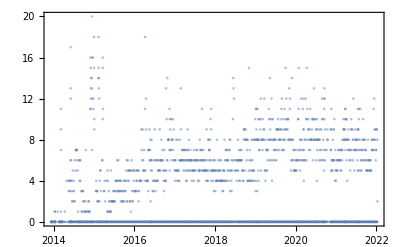

```mathematica
DateListPlot[deleteRedundantPoints[d[[All,{1,2}]],1000],PlotStyle->Opacity[0.5],Joined->False,PlotRange->All]
```

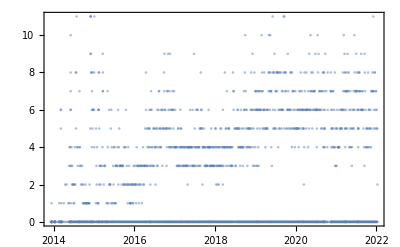

```mathematica
DateListPlot[deleteRedundantPoints[d[[All,{1,3}]],1000],PlotStyle->Opacity[0.5],Joined->False,PlotRange->All]
```

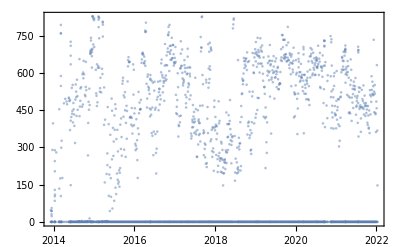

```mathematica
DateListPlot[deleteRedundantPoints[d[[All,{1,4}]],1000],PlotStyle->Opacity[0.5],Joined->False,PlotRange->All]
```

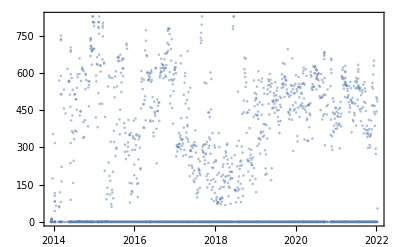

```mathematica
DateListPlot[deleteRedundantPoints[d[[All,{1,5}]],1000],PlotStyle->Opacity[0.5],Joined->False,PlotRange->All]
```

```mathematica
d1=Cases[d,{t_?NumberQ,mh_,mv_,ph_,pv_,phh_/;phh>4800,phv_,mch_/;mch<-1200,mcv_,bh_/;bh<-55,bv_,f_}:>{t,ph}];
```

```mathematica
Length@d1
```

3291234

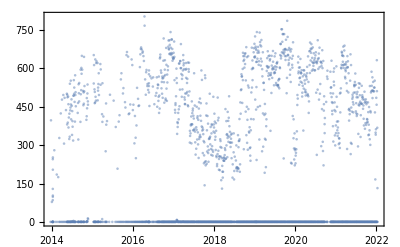

```mathematica
DateListPlot[deleteRedundantPoints[Cases[d,{t_?NumberQ,mh_,mv_,ph_,pv_,phh_/;phh>4800,phv_,mch_/;mch<-1200,mcv_,bh_/;bh<-55,bv_,f_}:>{t,ph}],1000],PlotStyle->Opacity[0.5],Joined->False,PlotRange->All]
```

```mathematica
paH=N@averageTheData[Cases[d,{t_?NumberQ,mh_,mv_,ph_,pv_,phh_/;phh>4800,phv_,mch_/;mch<-1200,mcv_,bh_/;bh<-55,bv_,f_}:>{t,ph}],60*95.];
```

```mathematica
paH5=N@averageTheData[Cases[d,{t_?NumberQ,mh_,mv_,ph_,pv_,phh_/;phh>4800,phv_,mch_/;mch<-1200,mcv_,bh_/;bh<-55,bv_,f_}:>{t,ph}],60*5.];
```

```mathematica
ff=Export[FileNameJoin[{NotebookDirectory[],"test.txt"}],paH,"Table"]
```

/Users/john/src/tiim.dck/example/test.txt

```mathematica
paV=N@averageTheData[Cases[d,{t_?NumberQ,mh_,mv_,ph_,pv_,phh_,phv_/;phv>4800,mch_,mcv_/;mcv<-1200,bh_,bv_/;bv<-55,f_}:>{t,pv}],60*95.];
```

```mathematica
paV5=N@averageTheData[Cases[d,{t_?NumberQ,mh_,mv_,ph_,pv_,phh_,phv_/;phv>4800,mch_,mcv_/;mcv<-1200,bh_,bv_/;bv<-55,f_}:>{t,pv}],60*5.];
```

```mathematica
ffV=Export[FileNameJoin[{NotebookDirectory[],"testV.txt"}],paV,"Table"]
```

/Users/john/src/tiim.dck/example/testV.txt

```mathematica
FileByteCount@ff
```

627034

```mathematica
a=Import[ff,"Table"];
```

```mathematica
b=Import[ffV,"Table"];
```

```mathematica
a//Length
```

19390

```mathematica
b//Length
```

19413

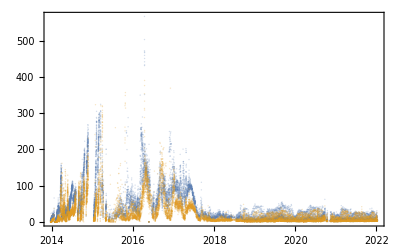

```mathematica
DateListPlot[{a,b},Joined->False,PlotStyle->Directive[AbsolutePointSize[1.],Opacity[.25]],PlotRange->All]
```

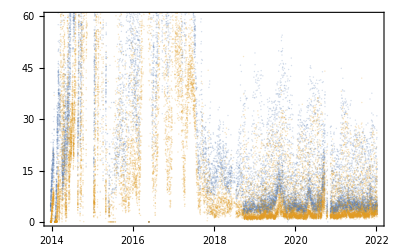

```mathematica
DateListPlot[{a,b},Joined->False,PlotStyle->Directive[AbsolutePointSize[1.],Opacity[.25]],PlotRange->{0,60}]
```

```mathematica
DateListPlot[{paH5,paV5},Joined->False,PlotStyle->Directive[AbsolutePointSize[1.],Opacity[.05]],PlotRange->{0,60}]
```

-Graphics-

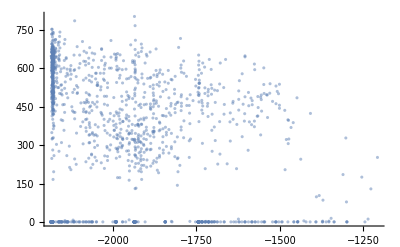

```mathematica
ListPlot[deleteRedundantPoints[Cases[d,{t_?NumberQ,mh_,mv_,ph_,pv_,phh_/;phh>4800,phv_,mch_/;mch<-1200,mcv_,bh_/;bh<-55,bv_,f_}:>{mch,ph}],1000],PlotStyle->Opacity[0.5],PlotRange->All]
```

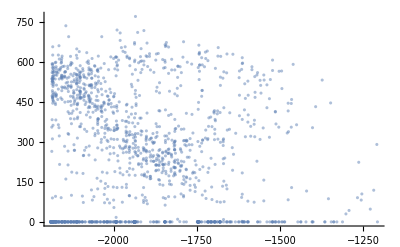

```mathematica
ListPlot[deleteRedundantPoints[Cases[d,{t_?NumberQ,mh_,mv_,ph_,pv_,phh_,phv_/;phv>4800,mch_,mcv_/;mcv<-1200,bh_,bv_/;bv<-55,f_}:>{mcv,pv}],1000],PlotStyle->Opacity[0.5],PlotRange->All]
```

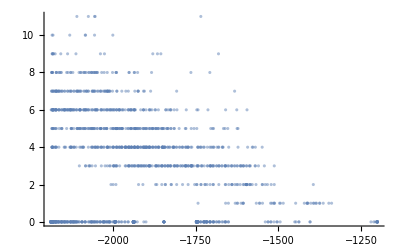

```mathematica
ListPlot[deleteRedundantPoints[Cases[d,{t_?NumberQ,mh_,mv_,ph_,pv_,phh_,phv_/;phv>4800,mch_,mcv_/;mcv<-1200,bh_,bv_/;bv<-55,f_}:>{mcv,mv}],1000],PlotStyle->Opacity[0.5],PlotRange->All]
```

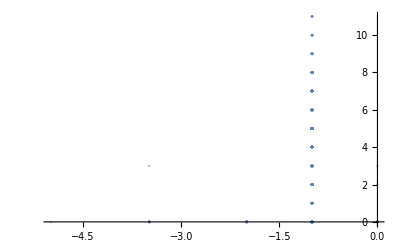

```mathematica
ListPlot[deleteRedundantPoints[Cases[d,{t_?NumberQ,mh_,mv_,ph_,pv_,phh_,phv_/;phv>4800,mch_,mcv_/;mcv<-1200,bh_,bv_/;bv<-55,f_}:>{f,mv}],1000],PlotStyle->Opacity[0.5],PlotRange->All]
```

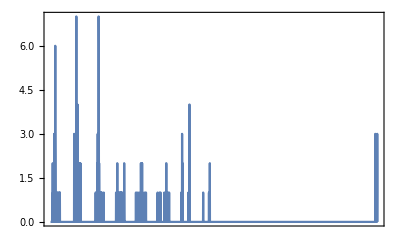

```mathematica
DateListPlot[d[[All,{1,3}]]]
```

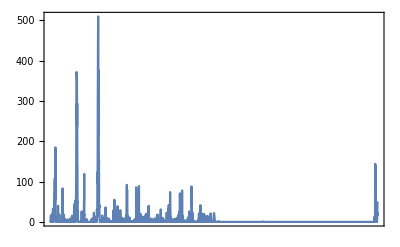

```mathematica
DateListPlot[d[[All,{1,4}]],PlotRange->All]
```

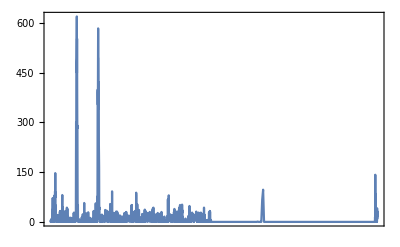

```mathematica
DateListPlot[d[[All,{1,5}]],PlotRange->All]
```

```mathematica
DateListPlot[d[[All,{1,5}]],PlotRange->All]
```

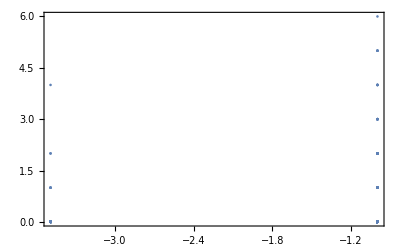

```mathematica
ListPlot[d[[All,{-1,2}]],Frame->True,PlotRange->All]
```

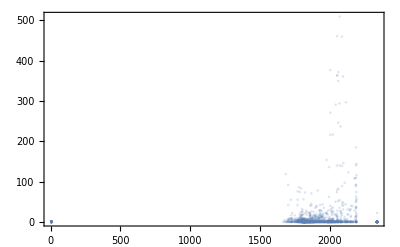

```mathematica
ListPlot[d[[All,{8,4}]]/.{v_,p_}:>{Abs[v],p},Frame->True,PlotRange->All,PlotStyle->Opacity[0.2]]
```

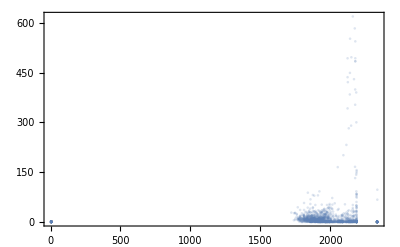

```mathematica
ListPlot[d[[All,{9,5}]]/.{v_,p_}:>{Abs[v],p},Frame->True,PlotRange->All,PlotStyle->Opacity[0.2]]
```

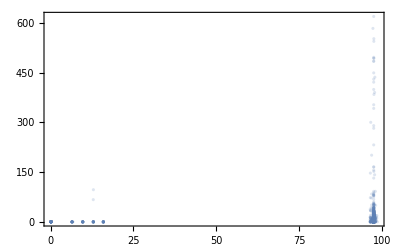

```mathematica
ListPlot[d[[All,{11,5}]]/.{v_,p_}:>{Abs[v],p},Frame->True,PlotRange->All,PlotStyle->Opacity[0.2]]
```

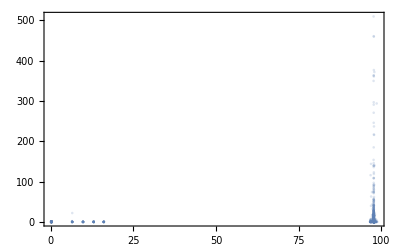

```mathematica
ListPlot[d[[All,{10,4}]]/.{v_,p_}:>{Abs[v],p},Frame->True,PlotRange->All,PlotStyle->Opacity[0.2]]
```